(3/2 | 1/2
-1/2 | 1/2) = (1 | 1
-1 | 1)(1 | 1
0 | 1)(1/2 | -1/2
1/2 | 1/2)

1

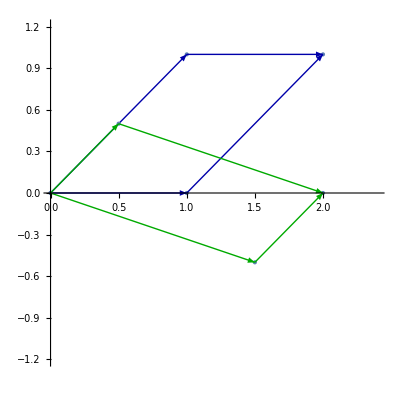

```mathematica
ClearAll[ m, j, e, ie,p, plotp ]

j = {{1, 1},{0,1}};
e = {{1,1},{-1,1}};
ie =  Inverse[e] ;
m = e . j . ie;

{
m // MatrixForm,
" = ",
e // MatrixForm,
j // MatrixForm,
ie // MatrixForm} // Row
Det[m]

plotp[m_, c_] := Module[{v1, v2,o},
{v1, v2} = m // Transpose ;
o = {0,0};
Show[{
ListPlot[ {o,v1, v2, v1 + v2}, 
AspectRatio->Automatic,
PlotStyle->PointSize[Large],
PlotRange ->{{0,2.4},{-1.2,1.2}}
],
Graphics[{
c,
Thick,
Arrow[{o,v1}],
Arrow[{o,v2}],
Arrow[{v1,v1 +v2}],
Arrow[{v2,v1 + v2}]
}]
}]
];

p = Show[{plotp[j, Blue // Darker],
plotp[m, Green // Darker]}]
```

```mathematica
<< peeters`;
peeters`setGitDir["../project/figures/ece1505-convex-optimization"]
```

/Users/pjoot/project/figures/ece1505-convex-optimization

```mathematica
peeters`exportForLatex[ "ps1p6dParallelogramsFig1", p]
```

{ps1p6dFig1.eps,ps1p6dFig1pn.png}